# 1. Gravity Tunnel in the Earth

## 1.1 Densities definition

### 1.1.1 Effective density function

First, we define the value of the constants that we are going to use: Acceleration of gravity, radius of the Earth, mean density of the Earth and gravity constant:

```mathematica
g=9.8156;  (*m/s2*)  
R=6.371 10^6; (*m*) 
ρ0 = 5513 ; (*kg/m3*)
G = 6.67 10^(-11) ;(* N m2/kg^2*)
```

We want to build a function of the following form

ρ1(r; b, c, d)=b ρ 0 (1-c r/R)^d

being b,c,d parameters to determine. It can be written in the code as the function

```mathematica
ρ 1[r_,b_,c_,d_]:=ρ0 b Power[1-c r/R,d]
```

this density have the following forms

```mathematica
Manipulate[Plot[ρ 1[r,b,c,d],{r,0,R},PlotStyle-> RGBColor[b,c,d]],{b,0.2,4,0.2},{c,0.1,1,0.1},{d,0.1,1,0.1}]
```

Plot::plln: Limiting value R in {r,0,R} is not a machine-sized real number.

#### 1.1.1.1 Effective density functions from PREM

Now, we have the next conditions to determine parameters b,c,d:

Density in the center of the Earth: ρ(0)=ρ_0 b =13088.5

then

```mathematica
b = 13088.5/ρ0 ;
Print["b = ", b]
```

b = 2.37325

Density at the surface must be that of the water (1000kg/m^2):  ρ(r = R) = b ρ_0(1-c )^d = ρ_R

then

(1-c)^d=0.1813/2.37325 = 0.076393

The third conditions is given from the total mass, we must have

M_T = 4π ∫_0^R ρ(r)r^2 ⅆr = 4π ρ_0 b∫_0^R (1 - c r/R)^d r^2 ⅆr

Doing the integral in Mathematica gives the analytical expression

```mathematica
Clear[b,R]
 Integrate[b*x^2*(1-c*(x/R))^d,{x,0,R}]
```

ConditionalExpression[(b (2+(1-c)^d (-1+c) (2+c (1+d) (2+c (2+d)))) R^3)/(c^3 (1+d) (2+d) (3+d)), Re[c]≤1||c∉ℝ]

so we can express the third condition as:

```mathematica
7.1197*(2-(1-x)^(y+1)(2+2x(1+y)+x^2(2+3y+y^2)))/(x^3*(6+11*y+6*y^2+y^3))-1
```

3 b [ 2 -  (1-c)^(d+1)(2+2c(1+d)+c^2(2+3d + d^2))]=  c^3(6 + 11d + 6 d^2+ d^3)

To solve the system of equations (1) and (3), this would be the code on Mathematica to solve the system, but it takes too long

```mathematica
Remove[x,y];
NSolve[{(1-x)^y==0.0763,7.1197(2-(1-x)^(y+1)*(2+2*x*(1+y)+x^2*(2+3*y+x^2)))/(x^3*(6+11*y+6*y^2+y^3))==1},{x,y}]
```

On the other hand, the next code on Python finds the answer in a few seconds:

from scipy.optimize import root

def equations(p):
	x, y  = p
	eq1 = (1-x)**y - 0.0763
	eq2 = 7.12*(2 - (1 - x)**(y + 1)*(2 + 2*x*(1 + y) + x**2*(2 + 3*y + y**2))) / (x**3*(6 + 11*y + 6*y**2 + y**3)) - 1
	return ( eq1 , eq2 )
	
sol =  root(equations, (0.1, 0.1), method='lm', jac=None, tol=None, callback=None, options={'col_deriv': 0, 'xtol': 1.49012e-08, 'ftol': 1.49012e-08, 'gtol': 0.0, 'maxiter': 0, 'eps': 0.0, 'factor': 100, 'diag': None})


x = sol.x[0]
y = sol.x[1]

#print(equations((x, y)))
print('x = ', x)
print('y = ', y)

x = 0.9875151202043234
y = 0.5867499795022912

For simplicity, the density function to work from here on is then

```mathematica
b = 2.37325;
c = 0.9875151202043234;
d = 0.5867499795022912;
ρ[r_]:=ρ 1[r,b,c,d]
```

Plotting with this result gives

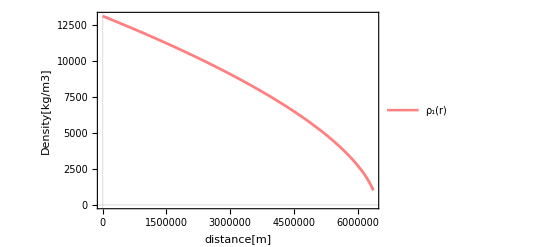

```mathematica
EffctiveFunction=Plot[{ρ[x]},{x,0,R},
PlotLegends->Placed[{"ρ_1(r)"},{Right,Top}],
PlotStyle->{Thickness[0.005],Pink},
Frame->True,
FrameLabel->{{"Density[kg/m3]",None},{"distance[m]",None}},
PlotTheme->"Scientific"]
```

#### 1.1.1.2 Numerical density from PREM

Now, let’s import PREM data and plot to see how this distribution looks like

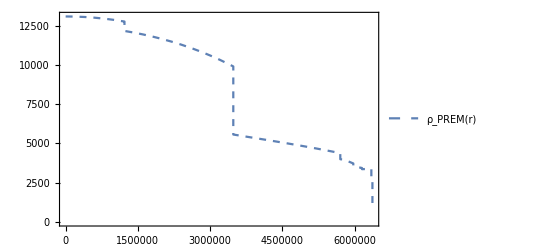

```mathematica
data=Import["/home/nicolas/Documents/Physics/Bachelors-Dissertation/1-Earth Gravity Tunnel/Numerical Data/prem-density.csv","Table"];
density prem=ListLinePlot[data,
PlotLegends->Placed[{"ρ_PREM(r)"},{Right,Top}],
PlotStyle->Dashed,
Frame->True
(*FrameLabel->{{"ρ_PREM[kg/m3]",None},{"r [m]",None}}*)]
```

```mathematica
Export["/home/nicolas/Documents/Physics/Bachelors-Dissertation/1-Earth Gravity Tunnel/Plots/density_prem.pdf",density prem];
```

To compare, we can plot them together

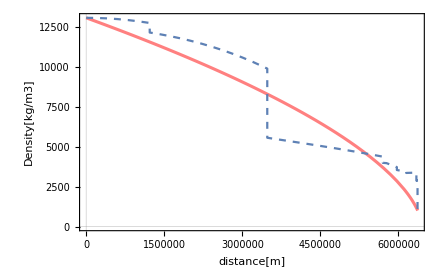

```mathematica
densities = Show[EffctiveFunction,density prem]
```

we see that actually the proposed functions fit between the data.

```mathematica
Export["/home/nicolas/Documents/Physics/Bachelors-Dissertation/1-Earth Gravity Tunnel/Plots/1-densities.pdf",densities];
```

### 1.1.2 Numerical Checks for the Effective Density Function

#### 1.1.2.1 Masses

Now, we want to determine the mass as a function of the radius. At r=R we would like to have M(r) = M ~ 6 x 10^15,

```mathematica
M[r_]:= 4 π  NIntegrate[ρ[x] x^2,{x,0,r}]
```

the output at the radius is

```mathematica
Print[Style["M_T = ",20],Style[M[R],20], Style[" kg",20,Italic]]
```

M_T = 5.97237×10^24 kg

the expected one.  To see the behaviour at any other point let’s plot this functions

```mathematica
Masses = Plot[{M[r]},{r,0,R},
PlotStyle->{{Thickness[0.008],Pink}},
Frame->True,
FrameLabel->{{"M(r) [kg]",None},{"r [m]",None}}]
```

-Graphics-

```mathematica
Export["/home/nicolas/Documents/Physics/Bachelors-Dissertation/1-Earth Gravity Tunnel/Plots/2-masses.pdf",Masses];
```

#### 1.1.2 Gravity

From density functions, we can compute it as

a(r) = (4π G)/r^2∫_0^r ρ(r')r'^2 ⅆr'

As this is the same integral of the mass, we have already compute analytically with Mathematica,  ‘til any point r, this gives

```mathematica
Clear[b,c,d,R]
Integrate[x^2*(1-c*(x/R))^d,{x,0,r}]
```

ConditionalExpression[(2 R^3+(1-(c r)/R)^d (c r-R) (c^2 (1+d) (2+d) r^2+2 c (1+d) r R+2 R^2))/(c^3 (1+d) (2+d) (3+d)), ]

Now, let’s define the function as

```mathematica
a analytic [r_]:= 3 g b (2 R^2-(1-c r/R)^(d+1)(c^2(1+d)(2+d)r^2 + 2c(1+d)r R + 2 R^2))/(c^3r^2(6 + 11d + 6 d^2+ d^3))
```

At the  radius the gravity is

```mathematica
Print[Style["g_analytic = ",20],Style[a analytic[R],20], Style[" m/s^2",20,Italic]]
```

g_analytic = 9.81567 m/s^2

As it should be. In terms of the binomial theorem, this can be made also analytically as

a (r) = (4π G)/r^2 ρ_0 b∫_0^r (1- c r'/R)^d r'^2 ⅆr' = (4π G)/r^2 (3M)/(4π R^3)∑_(n=0)^∞ (d
n)(-c)^n/R^n∫_0^r r^(n+2)ⅆr
	= 3 g b  ∑_(n=0)^∞ (d
n)(-c)^n/(n+3) (r/R)^(n+1)

in the code

```mathematica
a[r_]:=3 b g Sum[QBinomial[d,n,1] (-c)^n(r/R)^(n+1)/(n+3),{n,0,Infinity}]
```

at the surface we have

```mathematica
Print[Style["g = ",20],Style[a[R],20], Style[" m/s^2",20,Italic]]
```

g = 9.81667 m/s^2

which is a little above the expected value. 
We can both functions in the hole range by making plots

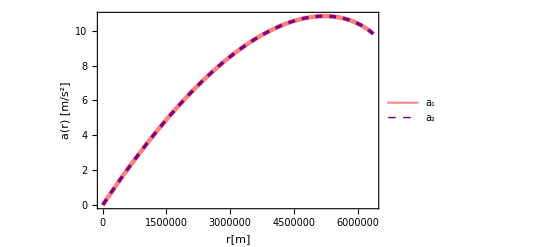

```mathematica
AccelerationFunctions=Plot[{a analytic[r],a[r]},{r,0,R},
PlotLegends->Placed[{"a_1","a_2"},{Right,Bottom}],
PlotStyle->{{Thickness[0.008],Pink},{Purple,Thickness[0.006],Dashed}},
Frame->True,
FrameLabel->{{"a(r) [m/s^2]",None},{"r[m]",None}}]
```

We see now that they are indeed the same.

#### From Prem

Here we write the official data in the pertinent units and interpolate it to have a continuous function

```mathematica
gravity prem = Import["/home/nicolas/Documents/Physics/Bachelors-Dissertation/1-Earth Gravity Tunnel/Numerical Data/gravity_prem.csv","Table"];
g prem=Interpolation[gravity prem,InterpolationOrder->5]
```

InterpolatingFunction[…]

Now, we can plot the three functions together

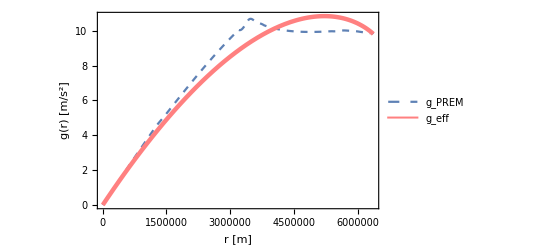

```mathematica
accelerations = Plot[{g prem[r],a[r]},{r,0,R},
PlotLegends->Placed[{"g_PREM","g_eff"},{Right,Bottom}],
PlotStyle->{Dashed,{Thickness[0.008],Pink}},
Frame->True,
FrameLabel->{{"g(r) [m/s^2]",None},{"r [m]",None}}]
```

```mathematica
Export["/home/nicolas/Documents/Physics/Bachelors-Dissertation/1-Earth Gravity Tunnel/Plots/3-accelerations.pdf",accelerations];
```

## 1.2 Velocity Profiles

Next, we are going to compute the velocities of the already found density profiles,

```mathematica
vprem[r_?NumberQ] := 10^(3/2)Sqrt[2*NIntegrate[g prem[x],{x,r,R}]](*√(2∫_r^R g prem[x]ⅆx) *)
v1[r_,b_]:=10^(3/2)Sqrt[2g/(k1[b]) Sum[QBinomial[b,k,1]*(-1)^k R^(-k-1) (R^(k+2)-r^(k+2))/((k+2)(k+3)),{k,0,10}]](*10^(3/2)√(2 g/k1[b]  ∑_(k=0)^10 (QBinomial[b,k,1](-1)^k R^(-(k+1)) (R^(k+2) - r^(k+2))/((k+2)(k+3))))*)
v2[r_,b_,c_]:=10^(3/2) Sqrt[2g/(k2[b,c]) Sum[QBinomial[b,k,1]*(-1-c)^k NIntegrate[(x/R)^(k+2)/(1+c x/R)^k R/y^2,{y,r,R},{x,0,y}],{k,0,10}]](*10^(3/2)√(2 g/k2[b,c]  ∑_(k=0)^10 (QBinomial[b,k,1](-1-c)^k ∫_r^R ∫_0^y (x/R)^(k+2)/(1+c x/R)^k   R/y^2 ⅆxⅆy))*)
```

we can here take some arbitrary values to have an idea of the closeness of the two functions and the expected value given by PREM

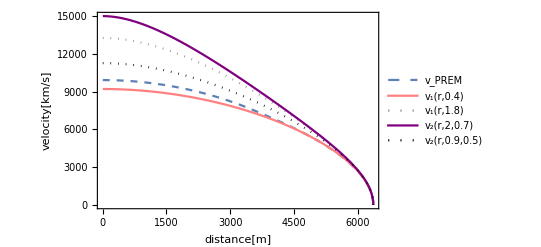

```mathematica
somevelocities = Plot[{vprem[x],v1[x,0.4 ],v1[x,1.8],v2[x,2,0.7],v2[x,0.9,0.5]},{x,0,R},
PlotLegends->Placed[{"v_PREM","v_1(r,0.4)","v_1(r,1.8)","v_2(r,2,0.7)","v_2(r,0.9,0.5)"},{Left,Bottom}],
PlotStyle->{Dashed,Pink,{Dotted,Gray},Purple,{Dotted,Black}},
Frame->True,
FrameLabel->{{"velocity[km/s]",None},{"distance[m]",None}}]
```

```mathematica
Export["/home/nicolas/Documents/Physics/Bachelors-Dissertation/Earth Gravity Tunnel/Plotssome-velocities.pdf",somevelocities];
```

For the optimum value found in the next section, we can compare the values for this velocities when the train is passing through the center of the Earth

```mathematica
{vprem[0],v1[0,0.5418],v2[0,0.55,4.26]}
```

{9914.73,9687.,10005.6}

but the best way to compare is with a plot

```mathematica
velocities = Plot[{vprem[x],v1[x,0.5418],v2[x,0.55,4.26]},{x,0,R},
PlotLegends->Placed[{"v_PREM","v_1","v_2"},{Right,Top}],
PlotStyle->{{ColorData[97][1],Dashed},{Thickness[0.004],Pink},{Purple,Thickness[0.008]}},
Frame->True,
FrameLabel->{{"velocity[m/s]",None},{"distance[m]",None}},
PlotTheme->"Scientific"]
```

let’s zoom in on a particular region

```mathematica
Plot[{vprem[x],v1[x,0.5418],v2[x,0.55,4.26]},{x,0.55 R,0.6 R},
PlotStyle->{Dashed,{Thickness[0.004],Pink},{Purple,Thickness[0.008]}},
Frame->True,
FrameTicks->None]
```

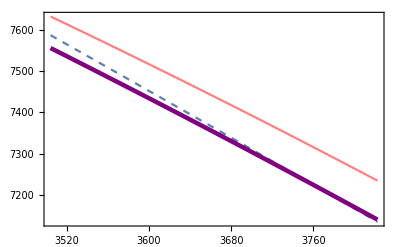

## 1.3 Minimization

Now, let’s find the best parameters for the description of the Earth’s interior, first, redefine the non-dimensional gravity profile

```mathematica
gravity prem ad=Import["/home/nicolas/Documents/Physics/Bachelors-Dissertation/1-Earth Gravity Tunnel/Numerical Data/prem-grav-ad.csv","Table"];
g prem ad=Interpolation[gravity prem ad];
```

with this we define the non-dimensional velocity

```mathematica
vprem ad[r_?NumberQ] := Sqrt[2*NIntegrate[ g prem ad[x], {x, r, 1}]]
```

Now define the non-dimensional version of the velocities

```mathematica
v1 ad[r_,b_,c_,d_]:=Sqrt[ b Sum[QBinomial[d,k,1]*(-c)^k  (1 - r^(k+2))/((k+2)(k+3)),{k,0,10}]]
(*v2 ad[r_?NumberQ,b_,c_]:=Sqrt[2/(k2[b,c]) Sum[QBinomial[b,k,1]*(-1-c)^k NIntegrate[x^(k+2)/(1+c x)^k 1/y^2,{y,r,1},{x,0,y}],{k,0,10}]]*)
```

They are all put into the functions to minimize, and can be directly minimized (can take a while)

```mathematica
f1[b_?NumericQ]:=NIntegrate[(1/v1 ad[r,b] - 1/vprem ad[r] )^2,{r,0,1},Method->"LocalAdaptive"];NMinimize[f1[b],{b},Method -> "NelderMead"]
```

{0.000425219,{b→0.541844}}

```mathematica
f2[b_?NumericQ,c_?NumericQ]:=NIntegrate[(1/v2 ad[r,b,c] - 1/vprem ad[r] )^2,{r,0,1},Method->"LocalAdaptive"];
NMinimize[f2[b,c],{b,c},Method -> "NelderMead"]
```

{0.0000253253,{b→9.13735,c→0.179943}}

```mathematica
f3[b_?NumericQ,c_?NumericQ]:=NIntegrate[(1/v3 ad[r,b,c] - 1/vprem ad[r] )^2,{r,0,1},Method->"LocalAdaptive"];
NMinimize[f3[b,c],{b,c},Method -> "NelderMead"]
```

## 1.4 Times chord path

We have arrived to the most important part of this work, the traversal time of the train.

```mathematica
T prem[d_]:= NIntegrate[x/(vprem ad[x]*Sqrt[x^2 - d^2 ]),{x,d,1}]
T1[d_]:= NIntegrate[x/(v1 ad[x,]*Sqrt[x^2 - d^2 ]),{x,d,1}]
(*T2[d_]:= NIntegrate[x/(v2 ad[x,0.55,4.26]*Sqrt[x^2 - d^2 ]),{x,d,1}]*)
```

SetDelayed::write: Tag Real in 3.67988[d_] is Protected.

$Failed

given the functions, we should check that the values for the tunnel across the center of the Earth are in some way close

```mathematica
{T prem[0],T1[0]}
```

{1.42206,3.67988[0]}

this means an error of

```mathematica
{(T prem[0]-T1[0])/(T prem[0])*100,(T2[0]-T prem[0])/(T prem[0])*100}
```

{0.243384,0.0435752}

But, again, the best way to compare the results is with a plot

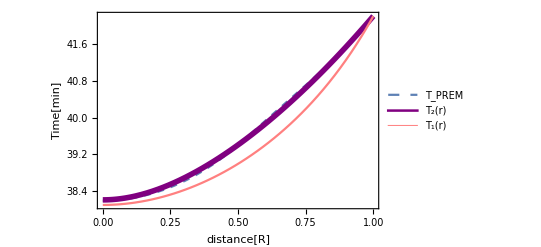

```mathematica
chordtimes = Plot[{T prem[x]*26.86259993217512, T2[x]*26.86259993217512,T1[x]*26.86259993217512},{ x,0,1},
PlotLegends->Placed[{"T_PREM","T_2(r)","T_1(r)"},{Left,Top}],
PlotStyle->{Dashed,{Purple,Thickness[0.01]},{Thickness[0.004],Pink}},
Frame->True,
FrameLabel->{{"Time[min]",None},{"distance[R]",None}}]
```

```mathematica
Export["/home/nicolas/Documents/Trabajo de Grado/Plots/times.pdf",chordtimes];
```

## 1.5 Brachistochrone

### 1.5.1 Shape of the brachistochrone curves

The other important part of this work is the time for the path of fastest descent and its shape. To find it we need first to define auxiliary functions for the integration,

```mathematica
I1[x_,d_]:=1/(Sqrt[x^4/(d)^2 *(v1 ad[d,0.5418]/v1 ad[x,0.5418])^2-x^2] )
I2[x_,d_]:=1/(Sqrt[x^4/(d)^2 *(v2 ad[d,0.55,4.26]/v2 ad[x,0.55,4.26])^2-x^2] )
I prem[x_,d_]:=1/(Sqrt[x^4/d^2 *(vprem ad[d]/vprem ad[x])^2-x^2] )
```

Now we can proceed to do the integration in a valid range

```mathematica
θ1 [r_?NumericQ,d_?NumericQ]:=If[r>d,NIntegrate[I1[x,d],{x,d,r}],0.0]
θ2 [r_?NumericQ,d_?NumericQ]:=If[r>d,NIntegrate[I2[x,d],{x,d,r}],0.0]
θ prem [r_?NumericQ,d_?NumericQ]:=If[r>d,NIntegrate[I prem[x,d],{x,d,r}],0.0]
```

In order to plot this in an appropriate way (maybe there is a better way), we need to extract some values

```mathematica
{FindRoot[θ1[1,d]- Pi/3,{d,0.1},AccuracyGoal->4,PrecisionGoal->4],
FindRoot[θ1[1,d]-Pi/6,{d,0.6},AccuracyGoal->4,PrecisionGoal->4]}
{FindRoot[θ2[1,d]-Pi/3,{d,0.1},AccuracyGoal->4,PrecisionGoal->4], 
FindRoot[θ2[1,d]-Pi/6,{d,0.6},AccuracyGoal->4,PrecisionGoal->4]}
{FindRoot[θ prem[1,d]-Pi/3,{d,0.1},AccuracyGoal->4,PrecisionGoal->4],FindRoot[θ prem[1,d]-Pi/6,{d,0.6},AccuracyGoal->4,PrecisionGoal->4]}
```

{{d→0.310287},{d→0.647024}}

{{d→0.298391},{d→0.63938}}

{{d→0.301061},{d→0.643903}}

```mathematica
braq13=Table[{θ1[i,0.310],i},{i,0.310,1,0.001}];
braq23=Table[{θ2[i,0.2984],i},{i,0.2984,1,0.001}];
braq16=Table[{θ1[i,0.647],i},{i,0.65,1,0.01}];
braq26=Table[{Re[θ2[i,0.639]],i},{i,0.640,1,0.001}];
braq prem3=Table[{θ prem[i,0.301],i},{i,0.301,1,0.001}];
braq prem6=Table[{Re[θ prem[i,0.6439]],i},{i,0.6439,1,0.001}];
```

Here we export them to plot the graphs more easily in gnuplot.

```mathematica
Export["braq13.csv",braq13,"Table"]
Export["braq16.csv",braq16,"Table"]
Export["braq23.csv",braq23,"Table"]
Export["braq26.csv",braq26,"Table"]
Export["braqprem3.csv",braq prem3,"Table"]
Export["braqprem6.csv",braq prem6,"Table"]
```

### 1.5.2 Times for the brachistochrone curves

In this subsection we are going to find the times found for the brachistochrone paths. As this are by definition the paths of fastest descent, the times should be the minimal times. To do this we need the derivative of the trajectory

```mathematica
Needs["NumericalCalculus`"]
```

```mathematica
ω1[r_, d_]:=D[θ1[x,d],x]/. x->r;
ω2[r_, d_]:=D[θ2[x,d],x]/. x->r;
ω prem[r_, d_]:=D[θ prem[x,d],x]/. x->r;
```

and  then the times for a given maximum approaching point d

```mathematica
Tbraq1[d_?NumericQ]:=NIntegrate[Sqrt[1+r^2 ω1[r,d]^2]/v1 ad[r,0.5418],{r,d,1}]
Tbraq2[d_?NumericQ]:=NIntegrate[Sqrt[1+r^2 ω2[r,d]^2]/v2 ad[r,0.55,4.26],{r,d,1}]
Tbraq prem[d_?NumericQ]:=NIntegrate[Sqrt[1+r^2 ω prem[r,d]^2]/vprem ad[r],{r,d,1}]
```

let’s check that the times taken when d=0 are the same as for the chord path

```mathematica
{Tbraq prem[0.4],Tbraq2[0.4],Tbraq1[0.4]}
```

NIntegrate::inumr: The integrand x^2/y^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1},{0,1}}.

NIntegrate::inumr: The integrand x^3/((1+4.26 x) y^2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1},{0,1}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

{1.30688,NIntegrate[(√(1+r^2 ω2[r,0.4]^2))/v2[r,0.55,4.26],{r,0.4,1}],1.30472}

they are almost the same, maybe it’s a question of precision, but we can trust in this results. We can see the complete dependence of the times on the position of the tunnel in the following plot

```mathematica
Plot[{Tbraq prem[x], Tbraq2[x],Tbraq1[x]},{ x,0,1},
PlotLegends->Placed[{"t_PREM","t_2(r)","t_1(r)"},{Left,Bottom}],
PlotStyle->{Dashed,Purple,Pink},
Frame->True,
FrameLabel->{{"Time[min]",None},{"distance[R]",None}}]
```

$Aborted

```mathematica
braqtimes=Plot[{Tbraq prem[x]*26.86259993217512, Tbraq2[x]*26.86259993217512,Tbraq1[x]*26.86259993217512},{ x,0,1},
PlotLegends->Placed[{"t_PREM","t_2(r)","t_1(r)"},{Left,Bottom}],
PlotStyle->{Dashed,Purple,Pink},
Frame->True,
FrameLabel->{{"Time[min]",None},{"distance[R]",None}}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.0383606}. NIntegrate obtained 1.43292+4.00407×10^-15 ⅈ and 0.0000728251 for the integral and error estimates.

$Aborted

```mathematica
Plot[{Tbraq prem[x]*26.86259993217512, Tbraq2[x]*26.86259993217512,Tbraq1[x]*26.86259993217512},{ x,0.7,0.8},
PlotLegends->Placed[{"t_PREM","t_2(r)","t_1(r)"},{Left,Bottom}],
PlotStyle->{Dashed,Purple,Pink},
Frame->True,
FrameLabel->{{"Time[min]",None},{"distance[R]",None}}]
```

$Aborted

```mathematica
Export["/home/nicolas/Documents/Trabajo de Grado/Plots/braqtimes.pdf",braqtimes];
```

## Accelerations

In this last section, we want give a dynamical reason for the difference between chord path times and brachistochrone path times. First, define some auxiliary functions

```mathematica
dist1[d_]:=Sqrt[1-(Sin[θ1[1,d]])^2]
dist2[d_]:=Sqrt[1-(Sin[θ2[1,d]])^2]
dist prem[d_]:=Sqrt[1-(Sin[θ prem[1,d]])^2]
```

Now we compute the radial accelerations

```mathematica
arad1[r_]:=1/k1[0.5418] * Sum[QBinomial[0.5418,k,1]*(-1)^k  r^(k+1)/(k+3),{k,0,10}];
arad2[r_]:=1/k2[0.55,4.26] * Sum[QBinomial[0.55,k,1]*(-1-4.26)^k  NIntegrate[(x)^(k+2)/(1+4.26 x)^k,{x,0,r}],{k,0,10}]/r^2;
arad prem=g prem ad;
```

with these and the auxiliary functions y can define the acceleration in the direction of motion for the chord path

```mathematica
a1[x_,d_]:=arad1[x]*Sqrt[x^2-(dist1[d])^2]/x
a2[x_,d_]:=arad2[x]*Sqrt[x^2-(dist2[d])^2]/x
a prem[x_,d_]:=arad prem[x]*Sqrt[x^2-(dist prem[d])^2]/x
```

as well as the acceleration in the direction of motion for the brachistochrone paths

```mathematica
abraq1[x_,d_]:=arad1[x]*Sin[θ1 [x, d]]
abraq2[x_,d_]:=arad2[x]*Sin[θ2 [x, d]]
abraq prem[x_,d_]:=arad prem[x]*Sin[θ prem[x, d]]
```

```mathematica
Table[abraq1[x,0.2],{x,0.3,1,0.01}]
```

{0.425022,0.447787,0.4697,0.490853,0.511316,0.531148,0.550396,0.5691,0.587291,0.604998,0.622242,0.639044,0.65542,0.671383,0.686947,0.702122,0.716915,0.731336,0.745389,0.759081,0.772415,0.785396,0.798026,0.810308,0.822244,0.833834,0.845079,0.85598,0.866536,0.876747,0.886612,0.89613,0.905298,0.914115,0.922578,0.930686,0.938434,0.945819,0.952838,0.959488,0.965762,0.971658,0.97717,0.982292,0.98702,0.991347,0.995266,0.998772,1.00186,1.00451,1.00673,1.00851,1.00983,1.01068,1.01107,1.01097,1.01037,1.00927,1.00765,1.0055,1.00281,0.999551,0.995722,0.991302,0.986275,0.980622,0.974326,0.967364,0.959715,0.951354,0.942244}

Now, let’s plot

```mathematica
accelerations1 =Plot[{Table[9.81*a2[x,d],{d,0.1,0.5,0.2}],Table[9.81*abraq1[x,d],{d,0.1,0.5,0.2}]},{x,0,1},
PlotRange->{0.0001,10.6},
PlotLegends->Placed[{"a_CHORD","a_BRAQ"},{Left,Top}],
PlotStyle->{Pink,Purple},
Frame->True,
FrameLabel->{{"acceleration[m/s2]",None},{"distance[R]",None}}]
```

$Aborted

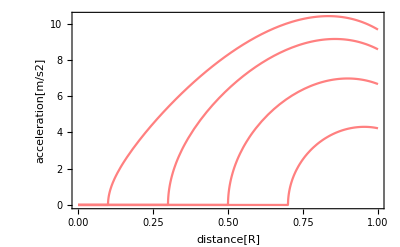

```mathematica
accelerations2 = Plot[Table[9.81*abraq1[x,d],{d,0.1,0.8,0.2}],{x,0,1},
PlotStyle->{Pink},
Frame->True,
FrameLabel->{{"acceleration[m/s2]",None},{"distance[R]",None}}]
```

```mathematica
a1 d01=Table[{x,9.81*abraq1[x,0.1]},{x,0.11,1,0.001}]
a1 d03=Table[{x,9.81*abraq1[x,0.3]},{x,0.11,1,0.001}];
a1 d05=Table[{x,9.81*abraq1[x,0.5]},{x,0.11,1,0.001}];
```

```mathematica
Export["/home/nicolas/Documents/Trabajo de Grado/Numerical Data/achord1d01.csv",a1 d01,"Table"];
Export["/home/nicolas/Documents/Trabajo de Grado/Numerical Data/achord1d03.csv",a1 d03,"Table"];
Export["/home/nicolas/Documents/Trabajo de Grado/Numerical Data/achord1d05.csv",a1 d05,"Table"];
```

Author: Nicolás Gómez Cruz

Appendix:

#### 1.1.1.1 Effective density functions from minimization of traversal times

In this case we are going to consider only conditions 2.  and 3., and the other condition would be to approximate traversal times of the chord path so that this is as closer as possible. So we have

Density at the surface must be that of the water (1000kg/m^2):  ρ(r = R) = b ρ_0(1-c )^d = ρ_R

b (1-c )^d = ρ_R/ρ_0=0.1813

Let’s use this to define b based on this

```mathematica
Clear[b,c,d]
B[c_,d_]:=0.1813/(1-c)^d
```

then, in the non-dimensional form

ρ(x;c,d)=0.1813 ((1-c x)/(1 -c))^d

Total mass

M_T = 4π ∫_0^R ρ(r)r^2 ⅆr = 4π ρ_0 b∫_0^R (1 - c r/R)^d r^2 ⅆr 
3 b [ 2 -  (1-c)^(d+1)(2+2c(1+d)+c^2(2+3d + d^2))]=  c^3(6 + 11d + 6 d^2+ d^3)

3 (0.1813/(1-c)^d) [ 2 -  (1-c)^(d+1)(2+2c(1+d)+c^2(2+3d + d^2))]=  c^3(6 + 11d + 6 d^2+ d^3)

To express the third condition, we need to compute the velocities, from density this is:

v(r)=√(8π G ∫_r^R ∫_0^y ρ(x;b,c,d)x^2 ⅆx 1/y^2 ⅆy)

Numerically, this is defined non-dimensionally as (the second is a developed expression using Newtons binomial theorem to spend computation time later)

```mathematica
Clear[b,c,d]
b = 0.1813/(1-c)^d;
v 1[r_,c_,d_]:= Sqrt[ NIntegrate[ b Power[1-c x,d]  x^2 /y^2,{y,r,1},{x,0,y}]]
v1 ad[r_,c_,d_]:=Sqrt[ b Sum[QBinomial[d,k,1]*(-c)^k  (1 - r^(k+2))/((k+2)(k+3)),{k,0,10}]]
```

```mathematica
v1 ad[0,b,0.98,d]*Sqrt[8 Pi G ρ0 R^2]
```

9851.77

Traversal times through the chord path, given by

T_1= 2∫_0^R 1/(v(r;b,c,d))ⅆr

programmatically, this is

```mathematica
{NIntegrate[b (1-c r/R)^d,{r,0,R}],R NIntegrate[b (1-c x)^d,{x,0,1}]}
```

{9.6406×10^6,9.6406×10^6}

```mathematica
T1 ad[b_,c_,d_]:=NIntegrate[1/v1 ad[r,b,c,d],{r,0,1}]
```

```mathematica
{T1 ad[b,c,d]}
```

{3.43248}

```mathematica
B[c_,d_]:=1/Sum[QBinomial[d,n,1] (-c)^n NIntegrate[x^(n+2),{x,0,1}],{n,0,10}];
ρ2[x_,c_,d_]:=B[c,d] (1-c x)^d
```

```mathematica
v2 ad[r_,c_,d_]:=Sqrt[2 B[c,d]*Sum[QBinomial[d,k,1]*(-c)^k  (1 - r^(k+2))/((k+2)(k+3)),{k,0,10}]]
gravity prem ad=Import["/home/nicolas/Documents/Physics/Bachelors-Dissertation/1-Earth Gravity Tunnel/Numerical Data/prem-grav-ad.csv","Table"];
g prem ad=Interpolation[gravity prem ad];
vprem ad[r_?NumberQ] := Sqrt[2*NIntegrate[ g prem ad[x], {x, r, 1}]]
```

```mathematica
f2[c_?NumericQ,d_?NumericQ]:=NIntegrate[(1/v2 ad[r,c,d] - 1/vprem ad[r] )^2,{r,0,1},Method->"LocalAdaptive"];
Constrain[c_,d_]:=B[c,d] (1-c)^d - 0.1813
A[c_,d_]:= 0.1813/(1-c)^d NIntegrate[(1- c x)^d x^2,{x,0,1}]
```

```mathematica
NMinimize[{f2[c,d], Constrain[c,d] ≤ 0.01},{c,d},Method -> "NelderMead"]
```

NMinimize::incst: NMinimize was unable to generate any initial points satisfying the inequality constraints {-0.1913+(1-c)^d/(0.333333-0.25 c d+0.1 Power[«2»] Plus[«2»] d-0.0277778 Power[«2»] Plus[«2»] Plus[«2»] d+0.00595238 Power[«2»] Plus[«2»] Plus[«2»] Plus[«2»] d-«1»+«1»-0.1 Power[«2»] Binomial[«2»]+0.0909091 Power[«2»] Binomial[«2»]-0.0833333 Power[«2»] Binomial[«2»]+«1»)≤0}. The initial region specified may not contain any feasible points. Changing the initial region or specifying explicit initial points may provide a better solution.

NMinimize::nrnum: The function value 0.0816159-0.625989 ⅈ is not a real number at {c,d} = {1.02842,0.559309}.

{0.000377119,{c→0.97571,d→0.609961}}

```mathematica
Constrain[0.9757,0.6099]
```

0.546756

```mathematica
Cd[0.99571,0.61]
```

0.0822573

```mathematica
f2[0.99571,0.60]
```

0.000542081

```mathematica
NMinimize[{f2[c,d], A[c,d]-1 ≤ 0.01},{c,d},Method -> "NelderMead"]
```

NIntegrate::inumr: The integrand x^2 (1-c x)^d has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NMinimize::nrnum: The function value 0.889517+0.000010743 ⅈ is not a real number at {c,d} = {2.2116,1.00612}.

{0.000275923,{c→0.918621,d→0.716689}}

```mathematica
Cd[0.9186,0.7166]
```

1.00052

```mathematica
A[0.9186,0.7166]
```

0.152891